# Physics through Computational Thinking

## Dynamics through Numerical Methods

Auditya Sharma and Ambar Jain

Dept. of Physics, IISER Bhopal

Outline

In this lecture you will

1. solve 2nd order differential equation for damped oscillation using Euler’s method

### Euler’s Method

For the differential equation of the type

ẋ(t)=f(x,t)
x(t_0)=x_0

we implemented Euler’s method using the Module/function below

```mathematica
euler[func_,xi_,ti_,tf_,nMax_]:=Module[{h,datalist,prev},
h=(tf-ti)/nMax//N;
For[datalist={{ti,xi}},                                            
Length[datalist]≤nMax,                                             
AppendTo[datalist,prev+{h,h  func@@prev}],     
prev=Last[datalist];                                                  
];
Return[datalist];
]
```

where, the input arguments are:

func: a function of t, x.  ẋ=func[t,x]

ti: initial time or start time for computation

tf: final time or end time for computation

xi: initial value of x at t=t_i.

nMax: number of time interval (or step size).

The expected local error in computation is of the order of h^2: 𝒪(h^2)

The expected global error in the computation is of the order of h: 𝒪(h)

We implemented the following err function to compute the mean global error given by equation

err=1/N∑_(i=1)^N |x_i-F(t_i)|

```mathematica
err[dataset_,func_]:=Module[{tlist,xlist,Fxlist},
tlist=dataset⟦;;,1⟧;             (*Extract each time value*)
xlist=dataset⟦;;,2⟧;             (*Extract each x value*)
Fxlist=func/@tlist;                 (*Apply func to each time value to get list of func[Subscript[t, i]]*)
Return[xlist-Fxlist//Abs//Mean];
]
```

Calculate the mean global error for various value of h for fixed t_i and t_f

```mathematica
f[t_,x_]=-x t;
ff[t_]=ⅇ^(-t^2/2);
Table[{5.0/10^n,err[euler[f,1,0,5,10^n],ff]/(5.0/10^n)},{n,1,4}]
```

{{0.5,0.0746396},{0.05,0.0639748},{0.005,0.0631697},{0.0005,0.0630899}}

```mathematica
err[euler[f,1,0,5,50],ff]
```

0.00648814

We see that the global error scales at h, thus the error is considered as 𝒪(h).

### Reducing Higher Order ODE to a set of first order ODEs

-Graphics-

The equations we are usually interested in solving are equation of motion, which are usually second order differential equation, such as

(ⅆ^2 Q)/(ⅆ t^2)=-Q/(L C)-R/L ⅆQ/ⅆt

associated with a suitable initial value condition like

Q(0)=Q_0
Q̇(0)=0

In order to apply a suitable numerical method, such as Euler’s method we will turn this IVP into a set of coupled first order ODEs:

ⅆQ/ⅆt=I
 ⅆI/ⅆt=-Q/(L C)-R/L I

Now this is set of two coupled ODEs of order 1, in terms of dynamical quantities Q and I, with initial condition:

Q(0)=Q_0
I(0)=0

We need to solve them simultaneously using Euler’s method.

### Generalization

Any n^thorder ODE can be converted to coupled n first order ODE. Let’s say ODE has the form:

ODE:   (ⅆ^n x)/(ⅆ t^n)=f(t,x,x^(1),x^(2),…,x^(n-1))

then, we can define

y=ẋ
z=ẏ
⋮
ṡ=w
ẇ=f(t,x,y,z,…,s,w)

which is a set of coupled ODEs

### Define and Translate LCR circuit eqn for Numerical Evaluation

Remember the four steps of Computational Thinking: Define, Translate, Compute and Interpret

In this problem we will define/identify and translate the problem into a form that it can be solved on the computer

First step is to non-dimensionalize the equation of motion for LCR circuit, thus reducing the number of parameters in the problem

Second step is to write the second order ODE into a set of first order ODEs (as shown in the previous section)

Problem: For the IVP given by equation below

(ⅆ^2 Q)/(ⅆ t^2)=-Q/(L C)-R/L ⅆQ/ⅆt
 Q(0)=Q_0
Q̇(0)=0

(a) Non-dimensionalize the equation by choosing suitable scales for Q, I and t, expressing the equation in dimensionless quantities.

(b) How many free parameters are left in the equation after non-dimensionalization?

(c) Write the non-dimensionalized equation as a set of first order ODEs.

(d) Express the solution of this equation in terms of your dimensionless quantities:

Q(t)=Q_0 ⅇ^(-R/(2L)t)cos(√(1/(L C)-R^2/(4 L^2))t)

### Solution

Q scale: | Q_0
t scale: | L/R
I scale: | Q_0 R/L

Making the transformation:

Q | ⟶ | Q_0 Q
t | ⟶ | L/R t
I | ⟶ | (Q_0 R)/L I

we get

Q_0/(L/R)^2(ⅆ^2 Q)/(ⅆ t^2)=-(Q_0 Q)/(L C)-R/L Q_0/(L/R)ⅆQ/ⅆt
⇒(ⅆ^2 Q)/(ⅆ t^2)=-L/(R^2 C)Q-ⅆQ/ⅆt

In the equation above, Q and t are dimensionless. Therefore, I=ⅆQ/ⅆt is also dimensionless. After non-dimensionalization, there is only one free parameter L/(R^2 C) which is the ratio of two competing time scales in the problem.

Writing as first order ODE we get

ⅆQ/ⅆt=I
ⅆI/ⅆt=-L/(R^2 C)Q-I
Q(0)=1
I(0)=0

The solution, in terms of dimensionless Q and t can be written as:

Q(t)=ⅇ^(-t/2)cos(√(L/(R^2 C)-1/4)t)

As expected, solution also depends only on one parameter: L/(R^2 C) which should be greater than 1/4 for the solution to be valid.

### Solving Coupled ODEs using Euler’s Method

Lets take the following set of coupled ODEs, which is most general case for ODE, as higher order ODEs can always be brought in similar form.

ẋ=f(t,x,y,z)
ẏ=g(t,x,y,z)
ż=h(t,x,y,z)

Define a column vectors X and F as

X=(t
x
y
z)  |     | F=(1
f
g
h)

Then the coupled ODEs can be written as

Ẋ=F

It is straightforward to generalize this to arbitrary dimensions as long as their is only one dynamical variable t.

Euler’s method is given by

X_0=X_initial
X_(n+1)=X_n+h F(X_n)

Here is its implementation. Notice the use of Through function

```mathematica
Through[{f,g,h}[x]]
```

{f[x],g[x],h[x]}

```mathematica
Through[{f,g,h}@x]
```

{f[x],g[x],h[x]}

```mathematica
Through[{f,g,h}@@{x,y}]
```

{f1[x,y],g[x,y],h[x,y]}

```mathematica
eulerGen[Func_,X0_,tf_,nMax_]:=Module[{h,datalist,prev,next,rate},
h=(tf-X0⟦1⟧)/nMax//N;
For[datalist={X0},                                            
Length[datalist]≤nMax,                                             
AppendTo[datalist,next],
prev=Last[datalist];
rate=Through[Func@@prev];
next=prev+h rate;
];
Return[datalist];
]
```

### Application to 2nd Order ODEs: LCR circuit

We want to solve the IVP:

ⅆQ/ⅆt=I
ⅆI/ⅆt=-L/(R^2 C)Q-I
Q(0)=1
I(0)=0

Implementation: Lets take the ratio w=L/(R^2 C)

```mathematica
w=10;
beta=√(w-1/4);
(2.0 π)/beta
id[t_,charge_,current_]=1;
chargeDot[t_,charge_,current_]=current;
currentDot[t_,charge_,current_]=-w charge-current;
initial={0,1,0};
```

2.01223

```mathematica
data=eulerGen[{id,chargeDot,currentDot},initial,10,10000];
```

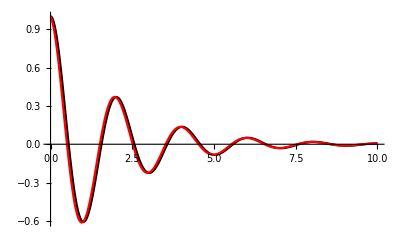

```mathematica
Show[ListPlot[data⟦;;,1;;2⟧,Joined->True,PlotMarkers->None,PlotRange->Full],Plot[ⅇ^(-t/2)Cos[beta t],{t,0,10},PlotRange->Full,PlotStyle->Red]]
```

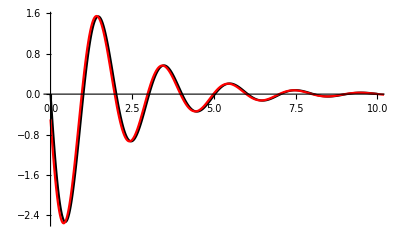

```mathematica
Show[ListPlot[data⟦;;,{1,3}⟧,Joined->True,PlotMarkers->None,PlotRange->Full],Plot[-1/2 ⅇ^(-t/2) Cos[t beta]-ⅇ^(-t/2) beta Sin[t beta],{t,0,20},PlotStyle->Red,PlotRange->Full]]
```